# QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Resonant_k\\QKT_full.wl"];
```

```mathematica
LaunchKernels[8];
```

## Grid

```mathematica
radius=2;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{20069,2}

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
GetQKTParityEigensystem[jParam_, alphaParam_, kParam_] :=
  Module[{mat, d, idx, matEven, matOdd, esEven, esOdd,
          phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,
          fullVecsEven, fullVecsOdd},
    mat = Floqsym[jParam, alphaParam, kParam];
    d = 2 jParam + 1;
    idx = ParitySectorIndices[jParam];
    matEven = mat[[idx["Even"], idx["Even"]]];
    matOdd  = mat[[idx["Odd"], idx["Odd"]]];
    esEven = Eigensystem[matEven, Method -> "Direct"];
    esOdd  = Eigensystem[matOdd, Method -> "Direct"];
    phEven = Mod[Arg[esEven[[1]]], 2 Pi];
    phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];
    idxE = Ordering[phEven]; idxO = Ordering[phOdd];
    vecsEven = esEven[[2, idxE]];
    vecsOdd  = esOdd[[2, idxO]];
    fullVecsEven = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];
    fullVecsOdd = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];
    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
                  "Phases" -> phEven,
                  "Vectors" -> vecsEven,
                  "FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]], 
                  "Phases" -> phOdd,
                  "Vectors" -> vecsOdd,
                  "FullVectors" -> fullVecsOdd|>|>
  ];
```

## Method

```mathematica
(*Floquet parameters*)
J =200; 
α=ArcTan[2.]; 
k=J*Pi(2/50.);
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31397 points...

```mathematica
Print["Computing Floquet matrix..."];
data=GetQKTParityEigensystem[J,α,k];
```

Computing Floquet matrix...

```mathematica
neweigenvec=Join[data["Even","FullVectors"],data["Odd","FullVectors"]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
```

-Graphics-

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
```

-Graphics-

## Husimis

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiValuesSorted=husimiValues;
```

```mathematica
(*should be 2J+1*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];
plot],{q,2J+1}];
```

```mathematica
α=ArcTan[2.];
```

```mathematica
jlist=Range[81,1000];
```

```mathematica
Do[
k=J*Pi(2/5.);
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"];
data=GetQKTParityEigensystem[J,α,k];
neweigenvec=Join[data["Even","FullVectors"],data["Odd","FullVectors"]];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
iprCompiled=Total[Abs[overlaps]^4,{1}];
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3];
Export["d2_resonant_J_"<>ToString[J]<>"_.png",plot];
,{J,jlist}];
```

$Aborted

# Anti coherence

## Definitions

```mathematica
(* ============================================================ *)
(*  ANTICOHERENCE DEFINITIONS — QKT PROJECT                     *)
(*  References:                                                  *)
(*    [DM22]  Denis & Martin, PRR 4, 013178 (2022)              *)
(*    [DLMS26] Denis et al., arXiv:2605.29436 (2026)            *)
(* ============================================================ *)
(* --- Multipole moments ρ_{LM} for a pure state vector ψ ---
   ψ is a length (2J+1) complex vector, components ordered m = -J,...,+J
   i.e. ψ[[k]] corresponds to m = -J + (k-1)
      From [DM22] Appendix A1:  [T_{LM}]_{m,m'} = Sqrt[(2L+1)/(2J+1)] * CG(J,m';L,M|J,m)
   Selection rule: m = m' + M, so the sum collapses to one index.
      Returns Association <| {L,M} -> ρ_{LM} |> for 0 ≤ L ≤ Lmax *)
Clear[stateMomentsSpinJ,mIdx,stateMomentsSpinJ];
stateMomentsSpinJ[J_, psi_, Lmax_] :=
  Module[{N = 2J + 1, mVals, rhoLM},
    mVals = Range[-J, J];
    Association @ Flatten @ Table[
      {L, M} -> Sqrt[(2L + 1) / N] *
        Sum[
          Conjugate[psi[[-J + J + mp + 1]]] *   (* ψ_{m'+M}^* ,  m = m'+M *)
          psi[[-J + J + mp + 1 - M]] *           (* ψ_{m'}      *)
          ClebschGordan[{J, mp}, {L, M}, {J, mp + M}],
          {mp, Max[-J, -J - M], Min[J, J - M]}   (* valid m' range *)
        ],
      {L, 0, Lmax}, {M, -L, L}
    ]
  ]

(* Cleaner index helper — maps m ∈ {-J,...,J} to array index *)
mIdx[J_, m_] := m + J + 1

stateMomentsSpinJ[J_, psi_, Lmax_] :=
  Module[{N = 2J + 1},
    Association @ Flatten @ Table[
      {L, M} -> Sqrt[(2L + 1) / N] *
        Sum[
          Conjugate[psi[[mIdx[J, mp + M]]]] * psi[[mIdx[J, mp]]] *
          ClebschGordan[{J, mp}, {L, M}, {J, mp + M}],
          {mp, Max[-J, -J - M], Min[J, J - M]}
        ],
      {L, 0, Lmax}, {M, -L, L}
    ]
  ]
```

```mathematica
(* --- Purity of the t-qubit reduced state via multipole moments ---
   From [DM22] Eq. (C9):
     Tr(ρ_t.b2) = Σ_{L=0}^{t} Σ_M  [(t!/N!).b2 * (N-L)!(N+L+1)!/((t-L)!(t+L+1)!)] |ρ_{LM}|.b2
   where N = 2J.  The L=0 term contributes exactly 1/(t+1). *)
Clear[reducedPurity];
reducedPurity[J_, moments_, t_] :=
  Module[{N = 2J, coeff},
    Sum[
      coeff = ((t!)^2 / (N!)^2) * ((N - L)! (N + L + 1)!) / ((t - L)! (t + L + 1)!);
      coeff * Sum[Abs[moments[{L, M}]]^2, {M, -L, L}],
      {L, 0, t}
    ]
  ]
```

```mathematica
(* --- Total purity-based t-anticoherence measure A^{T,P}_t ---
   From [DLMS26] Eq. (20) / [DM22] Eq. (23):
     A^{T,P}_t(ρ) = (t+1)/t * (1 - Tr(ρ_t.b2))
   = 0 for spin-coherent states, = 1 for t-anticoherent states *)
Clear[totalAC];
totalAC[J_, moments_, t_] :=
  (t + 1) / t * (1 - reducedPurity[J, moments, t])
```

```mathematica
(* --- Cumulative multipole weight C_{≤t} ---
   From [DLMS26] Eq. (40):  C_{≤t}(ρ) = Σ_{L=1}^{t} Σ_M |ρ_{LM}|.b2
   Note: L=0 term excluded (it is always 1/(2J+1) by normalization). *)
Clear[cumulativeMultipole];
cumulativeMultipole[moments_, t_] :=
  Sum[Abs[moments[{L, M}]]^2, {L, 1, t}, {M, -L, L}]
```

```mathematica
(* --- Total cumulative-multipole AC measure A^{T,cm}_t ---
   From [DLMS26] Eq. (42):  A^{T,cm}_t = 1 - C_{≤t}(ρ) / C_{≤t}(ρ_coh)
   Coherent-state reference value from [DLMS26] Eq. (41). 
   Valid for 1 ≤ t ≤ 2J-1. *)
Clear[coherentStateCumulativeMultipole,totalACcm];
coherentStateCumulativeMultipole[J_, t_] :=
  2J / (2J + 1) - ((2J)!)^2 / ((2J - t - 1)! (2J + t + 1)!)

totalACcm[J_, moments_, t_] :=
  1 - cumulativeMultipole[moments, t] / coherentStateCumulativeMultipole[J, t]
```

```mathematica
(* --- Parity check: for parity-definite states, odd-L moments vanish ---
   This is automatic from [F̂, P̂]=0, but useful to verify numerically. *)
Clear[parityCheck];
parityCheck[moments_, Lmax_] :=
  Max @ Table[
    If[OddQ[M], Abs[moments[{L, M}]], 0],
    {L, 1, Lmax}, {M, -L, L}
  ];
```

## Method

```mathematica
(* Example: compute AC measures for eigenvector index q, even sector *)
J = 20;
α = 0.84; 
k = 0.5;
data = GetQKTParityEigensystem[J, α, k];
```

```mathematica
(* Pick one full eigenvector *)
psi = Chop[data["Even", "FullVectors"][[2]]];   (* length 2J+1, full Hilbert space *)
```

```mathematica
(* Compute moments up to t_max = 6 (covers even orders t=2,4,6) *)
tMax = 10;
mom = stateMomentsSpinJ[J, psi, tMax];
```

```mathematica
{mom[{0,0}],1/Sqrt[2 J+1.]}
```

{0.156174,0.156174}

```mathematica
(* Verify: odd-rank moments should be ~0 for parity eigenstates *)
parityCheck[mom, tMax]   (* expect ~ machine epsilon *)
(* Purity-based total AC at even orders only *)
Table[{t, totalAC[J, mom, t]}, {t,tMax}]
(* Cumulative multipole AC at even orders only *)
Table[{t, totalACcm[J, mom, t]}, {t,tMax}]
```

0.

{{1,0.960931},{2,0.91847},{3,0.899605},{4,0.890392},{5,0.885473},{6,0.882627},{7,0.880849},{8,0.879637},{9,0.878716},{10,0.877931}}

{{1,0.960931},{2,0.85871},{3,0.871998},{4,0.881342},{5,0.875107},{6,0.875311},{7,0.87155},{8,0.858945},{9,0.854463},{10,0.838428}}

```mathematica
(* Pick one full eigenvector *)
psiodd = Chop[data["Odd", "FullVectors"][[2]]];   (* length 2J+1, full Hilbert space *)
```

```mathematica
(* Compute moments up to t_max = 6 (covers even orders t=2,4,6) *)
tMax = 10;
momodd=stateMomentsSpinJ[J, psiodd, tMax];
```

```mathematica
{momodd[{0,0}],1/Sqrt[2 J+1.]}
```

{0.156174,0.156174}

```mathematica
(* Verify: odd-rank moments should be ~0 for parity eigenstates *)
parityCheck[momodd, tMax]   (* expect ~ machine epsilon *)
(* Purity-based total AC at even orders only *)
Table[{t, totalAC[J, momodd, t]}, {t,tMax}]
(* Cumulative multipole AC at even orders only *)
Table[{t, totalACcm[J, momodd, t]}, {t,tMax}]
```

0.

{{1,0.287494},{2,0.386061},{3,0.462772},{4,0.522316},{5,0.568434},{6,0.604097},{7,0.631645},{8,0.652912},{9,0.669327},{10,0.681987}}

{{1,0.287494},{2,0.524784},{3,0.701914},{4,0.777531},{5,0.771743},{6,0.737094},{7,0.715585},{8,0.714717},{9,0.715737},{10,0.699401}}

# Anti coherence tests

## Definitions

```mathematica
(* ============================================================ *)
(*  ANTICOHERENCE — FAST VERSION                                 *)
(*  Strategy: precompute CG table, vectorize over eigenvectors  *)
(* ============================================================ *)

(* Build CG table once for fixed J, Lmax.
   cgTable[L, M] is a SparseArray of size (2J+1) indexed by mp,
   giving CG(J,mp; L,M | J, mp+M) for valid mp, zero elsewhere.
   Cost: O(Lmax^2 * J) ClebschGordan calls, done once. *)
Clear[buildCGtable,stateMomentsFromTable,reductionCoeffs,batchTotalAC];

buildCGtable[J_, Lmax_] :=
  Module[{dim = 2J + 1},
    Association @ Flatten @ Table[
      {L, M} -> SparseArray[
        Table[
          If[-J <= mp + M <= J,
            {mp + J + 1} -> N[ClebschGordan[{J, mp}, {L, M}, {J, mp + M}]],
            Nothing],
          {mp, -J, J}],
        {dim}],
      {L, 0, Lmax}, {M, -L, L}]
  ]

(* Compute all multipole moments for one state vector psi.
   Uses precomputed CG table — no ClebschGordan calls at runtime.
   rho_{LM} = Sqrt[(2L+1)/(2J+1)] * Conjugate[psi] . cgTable[L,M] * psi
   where the dot picks out the m = mp+M component. *)

stateMomentsFromTable[J_, psi_, cgTab_, Lmax_] :=
  Module[{N = 2J + 1, shifted},
    Association @ Flatten @ Table[
      {L, M} ->
        Sqrt[(2L + 1.) / N] *
          (* shift psi by M positions to align mp with mp+M *)
          Module[{shift = If[M >= 0,
              Join[ConstantArray[0., M], psi[[;; N - M]]],
              Join[psi[[1 - M ;;]], ConstantArray[0., -M]]]},
            Conjugate[psi] . (Normal[cgTab[{L, M}]] * shift)
          ],
      {L, 0, Lmax}, {M, -L, L}]
  ]

(* Batch version: compute totalAC for all eigenvectors at once.
   Returns a (nStates x tMax) matrix of A^{T,P}_t values.
   
   Key: reducedPurity only needs |rho_{LM}|^2 summed with known coefficients.
   Precompute the coefficient array once, then it's a dot product. *)

(* Precompute reduction coefficients c_{N,t,L} from [DM22] Eq.(C9) *)
reductionCoeffs[J_, tMax_] :=
  Module[{N = 2J},
    Table[
      If[L <= t,
        ((t!)^2 / (N!)^2) * (N - L)! * (N + L + 1)! / ((t - L)! * (t + L + 1)!),
        0.],
      {t, 1, tMax}, {L, 0, tMax}]
  ]

(* Main batch function: given list of state vectors, return AC table *)
batchTotalAC[J_, stateVecs_, tMax_] :=
  Module[{cgTab, coeffs, nStates = Length[stateVecs], moments, rhoSqByL},
    Print["Building CG table..."];
    cgTab = buildCGtable[J, tMax];
    coeffs = reductionCoeffs[J, tMax];   (* tMax x (tMax+1) matrix *)
    Print["Computing moments for ", nStates, " states..."];
    ParallelMap[
      Function[psi,
        (* moments: Association {L,M} -> complex number *)
        moments = stateMomentsFromTable[J, psi, cgTab, tMax];
        (* rhoSqByL[[L+1]] = sum_M |rho_{LM}|^2, for L=0..tMax *)
        rhoSqByL = Table[
          Total[Abs[moments[{L, #}]]^2 & /@ Range[-L, L]],
          {L, 0, tMax}];
        (* A^{T,P}_t = (t+1)/t * (1 - coeffs[t] . rhoSqByL) *)
        Table[
          (t + 1.) / t * (1. - coeffs[[t]] . rhoSqByL),
          {t, 1, tMax}]
      ],
      stateVecs
    ]
  ]
```

## Method

```mathematica
(* Run for all eigenvectors, J=100 *)
J =100; 
α=0.84; 
k=27.5;
data = GetQKTParityEigensystem[J, α, k];
allVecs = Join[data["Even","FullVectors"], data["Odd","FullVectors"]];
```

```mathematica
tMax = 10;
acTable = batchTotalAC[J, allVecs, tMax];
(* acTable[[i, t]] = A^{T,P}_t for eigenvector i at order t *)
```

Building CG table...

Computing moments for 201 states...

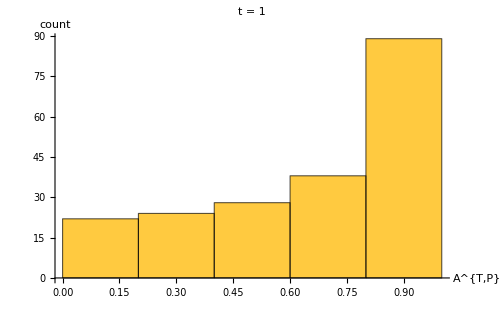
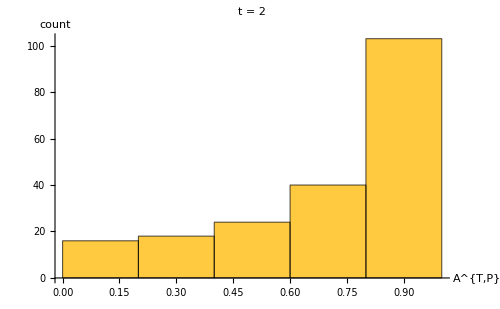
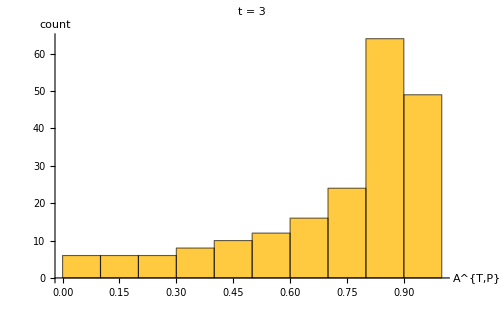
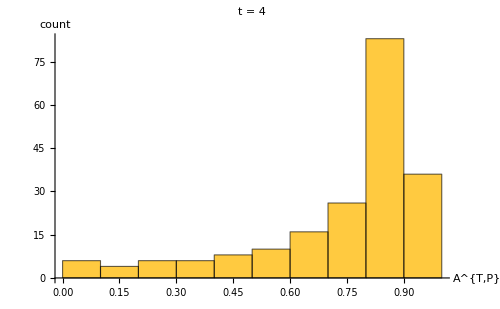
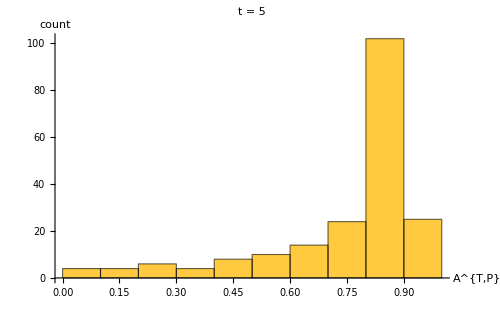
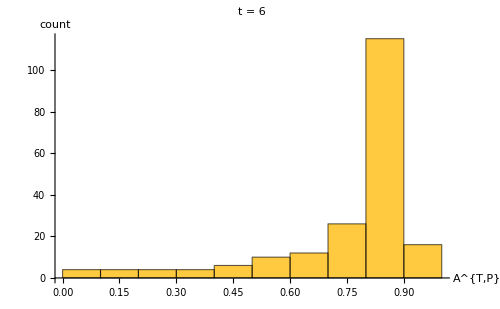
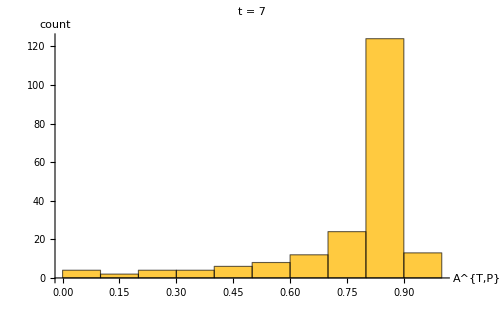
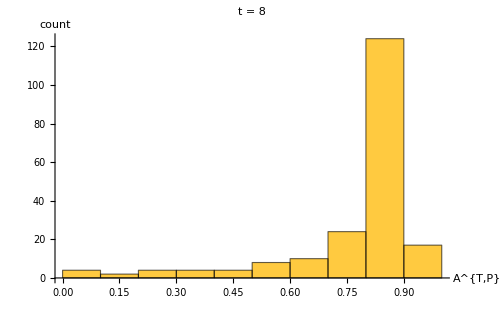

```mathematica
Table[
      Histogram[acTable[[All, t]],
        PlotLabel -> "t = " <> ToString[t],
        AxesLabel -> {"A^{T,P}", "count"},
        PlotRange -> {{0, 1}, All},ImageSize->500],
      {t, 1, tMax}]
```

```mathematica
cgTab=buildCGtable[J,tMax];
```

```mathematica
Abs[mom[{0,0}]]^2
1/(2J+1.)
```

0.00497512

0.00497512

```mathematica
(* Take an eigenvector from the chaotic regime *)
psi = allVecs[[50]];
mom = stateMomentsFromTable[J,psi,cgTab,tMax];
(* Print |rho_{LM}|^2 for each L *)
Table[
  {L, Table[Abs[mom[{L, M}]]^2, {M, -L, L}]},
  {L, 1, 6}
] //Chop//TableForm
```

1 | 0
2.41297×10^-6
0
2 | 0.000093999
0
0.000124503
0
0.000101595
3 | 0
9.29469×10^-6
0
0.000201693
0
0.0000101939
0
4 | 7.28678×10^-6
0
5.0357×10^-6
0
0.000124878
0
9.60796×10^-6
0
3.20766×10^-6
5 | 0
0.0000300663
0
0.0000328231
0
0.000273212
0
0.0000425035
0
0.0000546146
0
6 | 0.000134989
0
0.0000397971
0
0.0000721259
0
0.000141305
0
0.0000669716
0
0.0000289476
0
0.000145421

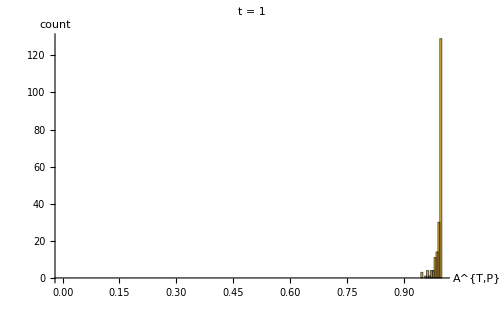
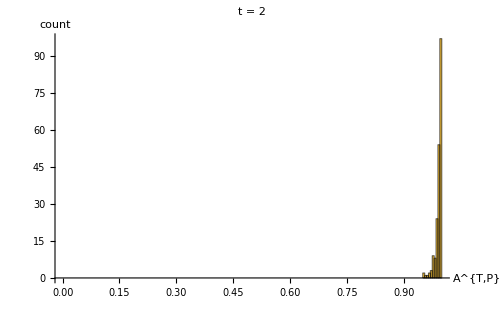
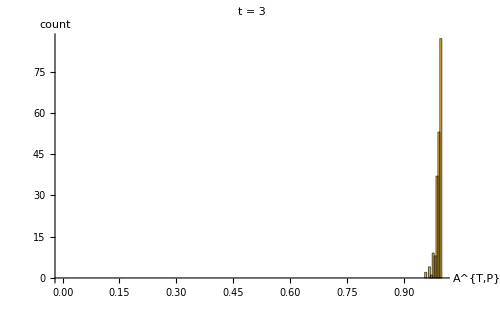
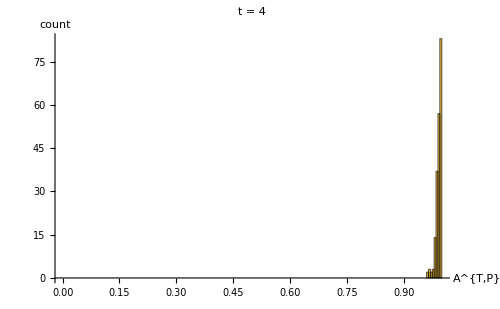
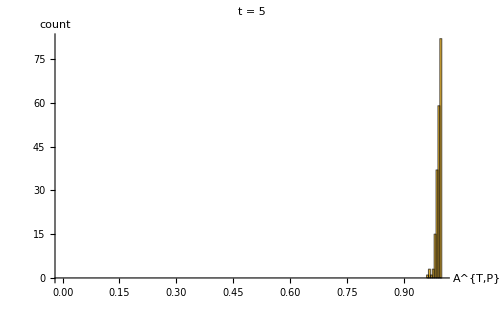
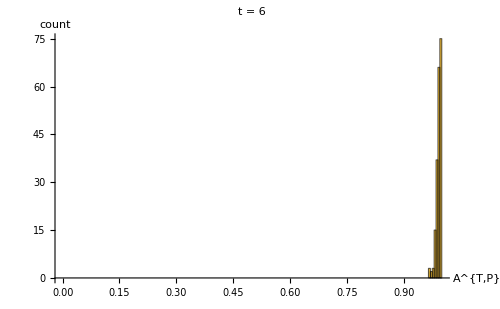
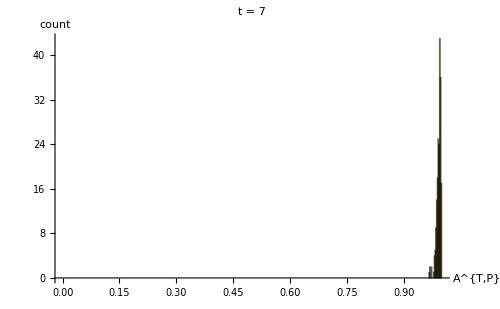
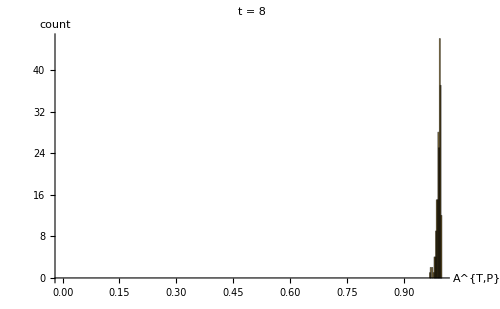

```mathematica
Table[
      Histogram[acTable[[All, t]],
        PlotLabel -> "t = " <> ToString[t],
        AxesLabel -> {"A^{T,P}", "count"},
        PlotRange -> {{0, 1}, All},ImageSize->500],
      {t, 1, tMax}]
```

```mathematica
cgTab=buildCGtable[J,tMax];
```

```mathematica
Abs[mom[{0,0}]]^2
1/(2J+1.)
```

0.00497512

0.00497512

```mathematica
(* Take an eigenvector from the chaotic regime *)
psi = allVecs[[50]];
mom = stateMomentsFromTable[J,psi,cgTab,tMax];
(* Print |rho_{LM}|^2 for each L *)
Table[
  {L, Table[Abs[mom[{L, M}]]^2, {M, -L, L}]},
  {L, 1, 6}
] //Chop//TableForm
```

1 | 0
2.41297×10^-6
0
2 | 0.000093999
0
0.000124503
0
0.000101595
3 | 0
9.29469×10^-6
0
0.000201693
0
0.0000101939
0
4 | 7.28678×10^-6
0
5.0357×10^-6
0
0.000124878
0
9.60796×10^-6
0
3.20766×10^-6
5 | 0
0.0000300663
0
0.0000328231
0
0.000273212
0
0.0000425035
0
0.0000546146
0
6 | 0.000134989
0
0.0000397971
0
0.0000721259
0
0.000141305
0
0.0000669716
0
0.0000289476
0
0.000145421

## Chaotic

## Method

```mathematica
(* Run for all eigenvectors, J=100 *)
J =100; 
α=ArcTan[2.]; 
k=J*Pi(2/50.)
data = GetQKTParityEigensystem[J, α, k];
allVecs = Join[data["Even","FullVectors"], data["Odd","FullVectors"]];
```

12.5664

```mathematica
tMax = 3;
AbsoluteTiming[acTable = batchTotalAC[J, allVecs, tMax];]
(* acTable[[i, t]] = A^{T,P}_t for eigenvector i at order t *)
```

Building CG table...

Computing moments for 201 states...

{2.20428,Null}

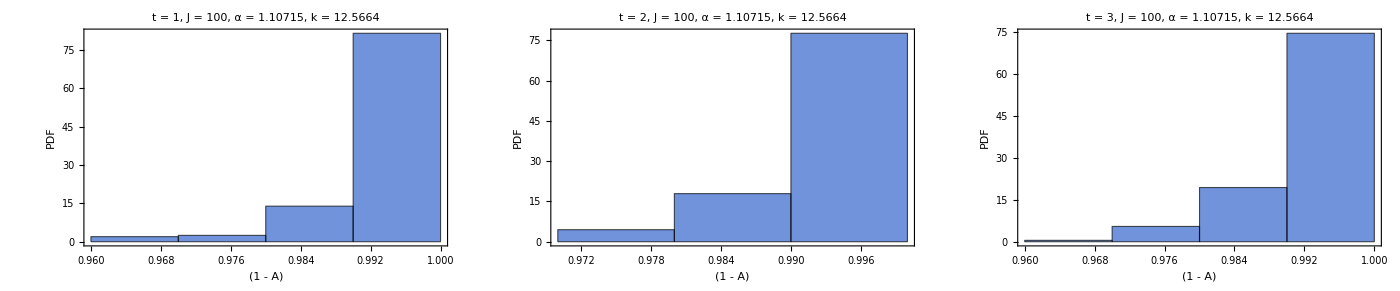

```mathematica
GraphicsGrid[
  Partition[
    Table[
      Histogram[
        acTable[[All, t]],{0.01},"PDF",
        PlotLabel->Style[Row[{"t = ",t,",  J = ",J,",  α = ",α,",  k = ",k}],12,Black],
        Frame -> True,
        FrameLabel->{{Style["PDF",11],None},{Style[Row[{"(1 - A)"}],11],None}},
        ChartStyle -> Directive[RGBColor[0.2, 0.4, 0.8], Opacity[0.7]],
        ImageSize -> 200,PlotRange->All],
      {t, 1, tMax}],
    UpTo[5]],
  Spacings -> {0.3, 0.3},
  ImageSize -> 1400]
```

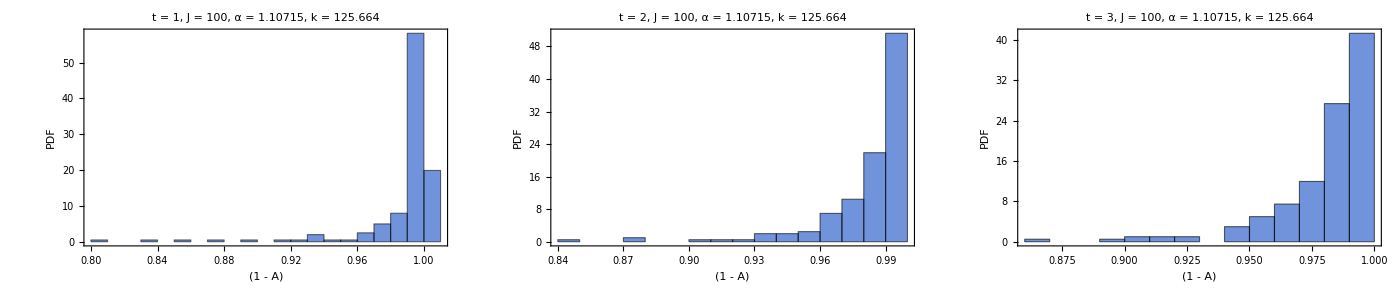

```mathematica
GraphicsGrid[
  Partition[
    Table[
      Histogram[
        acTable[[All, t]],{0.01},"PDF",
        PlotLabel->Style[Row[{"t = ",t,",  J = ",J,",  α = ",α,",  k = ",k}],12,Black],
        Frame -> True,
        FrameLabel->{{Style["PDF",11],None},{Style[Row[{"(1 - A)"}],11],None}},
        ChartStyle -> Directive[RGBColor[0.2, 0.4, 0.8], Opacity[0.7]],
        ImageSize -> 200,PlotRange->All],
      {t, 1, tMax}],
    UpTo[5]],
  Spacings -> {0.3, 0.3},
  ImageSize -> 1400]
```

```mathematica
(*GraphicsGrid[
  Partition[
    Table[
      Histogram[
        -Log10[1 - acTable[[All, t]] + 10^-15],
        Automatic, "PDF",
        PlotLabel->Style[Row[{"t = ",t,",  J = ",J,",  α = ",α,",  k = ",k}],12,Black],
        Frame -> True,
        FrameLabel->{{Style["PDF",11],None},{Style[Row[{"-",Subscript["Log","10"],"(1 - A)"}],11],None}},
        ChartStyle -> Directive[RGBColor[0.2, 0.4, 0.8], Opacity[0.7]],
        ImageSize -> 280,PlotRange->All],
      {t, 1, tMax}],
    5],
  Spacings -> {0.3, 0.3},
  ImageSize -> 1400]*)
```